Supplemental notebook to 
Richard  Herrmann, 
Fractional Calculus - Introduction for Physicists,
4th edition, 
World Scientific Publishing, Singapore. 
Chapter 9
https://www.worldscientific.com/worldscibooks/10.1142/14345#t=aboutBook

# Chapter 9: Step 2 : TrainModel

Richard Herrmann

gigaHedron, r.herrmann@fractionalcalculus.org

October 2024.

## Introduction

Mathematica notebook to train model. 
Prerequisites:   sound files: homeDirectory/soundAI/plus/*.wav  and homeDirectory/soundAI/minus/*.wav

## Program

### Prologue

```mathematica
(*start:Import the WAV file as an Audio object*)
enc=NetEncoder["AudioMFCC"];         (*audio encoder*)
method="LinearRegression";  (*choose training method*)
Print["starting with method: ",method];
plus=True;                             (*causal*)
minus=True; 
myFolder="soundML"
filePattern=FromCharacterCode[42]<>".wav"; (* = *.wav*)
homeDir=FileNameJoin[{$UserDocumentsDirectory,myFolder}]
modelName="Model"<>ToString[method]
modelFile=modelName<>".wl"; (*export and later use*)

SetDirectory[homeDir];
```

starting with method: LinearRegression

soundML

D:\DocumentsD\soundML

ModelLinearRegression

### Module SplitData : splits the data in training / test subset

```mathematica
SplitData[data_,trainFract_]:=Module[
{n=Length[data],indices,trainingIndices,testIndices},
(*Generate random indices and split them*)
indices=RandomSample[Range[n]];
trainingIndices=Take[indices,Round[n trainFract]];
testIndices=Drop[indices,Round[n trainFract]];
(*Return training and testing data*)
{data[[trainingIndices]],data[[testIndices]]}
];
```

### Module ExtractDelay : delay from file name

```mathematica
ExtractDelay[newFile_]:=Module[
{xctDelay,number},
number=StringCases[newFile,"Delay"~~num:NumberString~~"S":>num];
xctDelay=ToExpression[number[[1]]];
If[StringContainsQ[newFile,"MDelay"],xctDelay=-xctDelay];
Return[xctDelay]
];
```

### Module ExtractDelay : process sound files

```mathematica
LoadSndDat[directory_]:=Module[
{fileList,soundData},
fileList=FileNames[filePattern,directory];
soundData=({Import[#],ExtractDelay[#]}&)/@fileList;
{soundData[[All,1]],soundData[[All,2]]}
];
```

### Module GetFeatures : collect features

```mathematica
GetFeatures[tDirPlus_,tDirMinus_]:=Module[
{sound, delay, sndPlus={},sndMinus={},delayPlus={},delayMinus={},features},
(*Load all sound files from the plus/minus folder*)
If[plus,{sndPlus,delayPlus}=LoadSndDat[tDirPlus]];
If[minus,{sndMinus,delayMinus}=LoadSndDat[tDirMinus]];
sound=Join[sndPlus,sndMinus];(*stitch*)
delay=Join[delayPlus,delayMinus];
features=MapThread[{Flatten[enc[Audio[#1]]],#2}&,{sound,delay}];
Return[features];
];
```

### Module TrainAndSave : central train and save model

```mathematica
TrainAndSave[tDirPlus_,tDirMinus_,modelFile_,trainFract_:0.8]:=Module[
{features,trainingData,testingData,model,testResults},
(*Extract features and create full dataset*)
features=GetFeatures[tDirPlus,tDirMinus];
Print[Length[features]]
(*Split data into training and testing sets*)
{trainingData,testingData}=SplitData[features/. {feature_,delay_}:>feature->delay,trainFract];
(*Train the model on the training set*)
model=Predict[trainingData,Method->method];
(*Test the model on the testing set and evaluate*)
testResults=PredictorMeasurements[model,testingData];
(*Output the evaluation metrics*)
Print["ComparisonPlot:",testResults["ComparisonPlot"]];
(*Save the trained model to a file*)
Export[modelFile,model];
Print["Model saved to: ",modelFile];
];
```

### unit-test

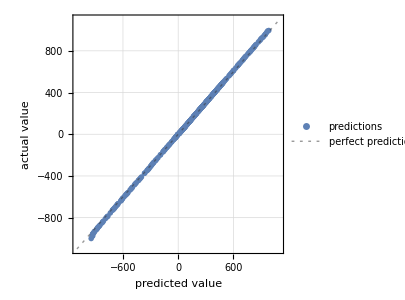
ComparisonPlot:-Graphics-

Model saved to: ModelLinearRegression.wl

```mathematica
modelName="Model"<>ToString[method];       
modelFile=modelName<>".wl";
(*unit test:Training and export*)
TrainAndSave["plus","minus",modelFile,0.5];
```